```mathematica
v="10";
p="0.1";
g5k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapD-l5k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v5k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/velD-l5k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av5k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/AveVel-l5k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number}];
g10k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapD-l10k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v10k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/velD-l10k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av10k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/AveVel-l10k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number}];g20k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapD-l20k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v20k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/velD-l20k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av20k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/AveVel-l20k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number}];g30k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapD-l30k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v30k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/velD-l30k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av30k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/AveVel-l30k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number}];
g40k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapD-l40k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v40k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/velD-l40k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av40k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/AveVel-l40k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number}];g50k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapD-l50k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v50k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/velD-l50k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av50k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/AveVel-l50k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number}];
```

```mathematica
ngap="3";
nvel="3";
jj=StringToStream[ngap];
ng= Read[jj,Number];
ii=StringToStream[nvel];
nv= Read[ii,Number];
ClearAll[d0,z,α];
d0=0.0674;
z=0.65;
α=0.65;
gap5v10=Table[{g5k1[[All,1]][[j]],Sum[g5k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g5k1]}];
vel5v10=Table[{v5k1[[All,1]][[j]],Sum[v5k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v5k1]}];
avel5v10=Table[{av5k1[[All,1]][[j]],av5k1[[All,2]][[j]]},{j,1,Length[av5k1]}];
gap10v10=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g10k1]}];
vel10v10=Table[{v10k1[[All,1]][[j]],Sum[v10k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v10k1]}];
avel10v10=Table[{av10k1[[All,1]][[j]],av10k1[[All,2]][[j]]},{j,1,Length[av10k1]}];
gap20v10=Table[{g20k1[[All,1]][[j]],Sum[g20k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g20k1]}];
vel20v10=Table[{v20k1[[All,1]][[j]],Sum[v20k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v20k1]}];
avel20v10=Table[{av20k1[[All,1]][[j]],av20k1[[All,2]][[j]]},{j,1,Length[av20k1]}];
gap30v10=Table[{g30k1[[All,1]][[j]],Sum[g30k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g30k1]}];
vel30v10=Table[{v30k1[[All,1]][[j]],Sum[v30k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v30k1]}];
avel30v10=Table[{av30k1[[All,1]][[j]],av30k1[[All,2]][[j]]},{j,1,Length[av30k1]}];
gap40v10=Table[{g40k1[[All,1]][[j]],Sum[g40k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g40k1]}];
vel40v10=Table[{v40k1[[All,1]][[j]],Sum[v40k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v40k1]}];
avel40v10=Table[{av40k1[[All,1]][[j]],av40k1[[All,2]][[j]]},{j,1,Length[av40k1]}];
gap50v10=Table[{g50k1[[All,1]][[j]],Sum[g50k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g50k1]}];
vel50v10=Table[{v50k1[[All,1]][[j]],Sum[v50k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v50k1]}];
avel50v10=Table[{av50k1[[All,1]][[j]],av50k1[[All,2]][[j]]},{j,1,Length[av50k1]}];
```

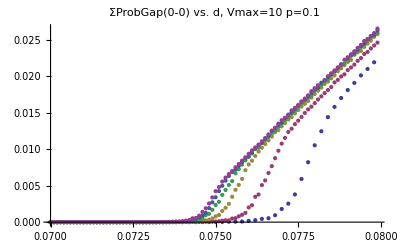

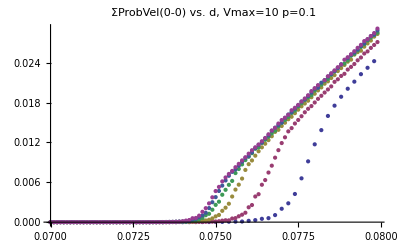

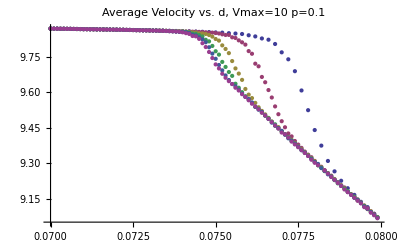

```mathematica
ListPlot[{gap5v10,gap10v10,gap20v10,gap30v10,gap40v10,gap50v10},PlotLabel->"ΣProbGap(0-"<>ngap<>") vs. d, Vmax="<>v<>"  p="<>p,PlotLegend->{"5k","10k","20k","30k","40k","50k"},LegendPosition->{1.1,-0.4},LegendShadow->None]
ListPlot[{vel5v10,vel10v10,vel20v10,vel30v10,vel40v10,vel50v10},PlotLabel->"ΣProbVel(0-"<>nvel<>") vs. d, Vmax="<>v<>"  p="<>p,PlotLegend->{"5k","10k","20k","30k","40k","50k"},LegendPosition->{1.1,-0.4},LegendShadow->None]
ListPlot[{avel5v10,avel10v10,avel20v10,avel30v10,avel40v10,avel50v10},PlotLabel->"Average Velocity vs. d, Vmax="<>v<>"  p="<>p,PlotRange->Full,PlotLegend->{"5k","10k","20k","30k","40k","50k"},LegendPosition->{1.1,-0.4},LegendShadow->None]
```

0.066

0.089

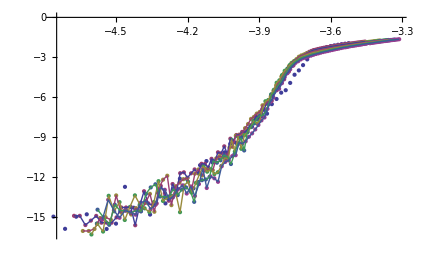

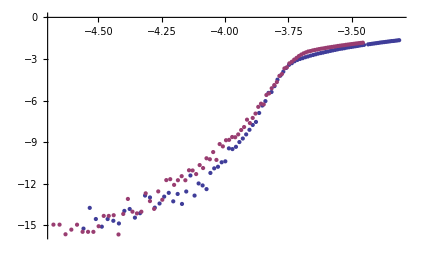

```mathematica
ClearAll[d0,z,α];
d0=0.066;
z=0.089;
α=0.089;

ga5k1=gap5v10[[All,1]];
ga10k1=gap10v10[[All,1]];
ga20k1=gap20v10[[All,1]];
ga30k1=gap30v10[[All,1]];
ga40k1=gap40v10[[All,1]];
ga50k1=gap50v10[[All,1]];

ga5k2=gap5v10[[All,2]];
ga10k2=gap10v10[[All,2]];
ga20k2=gap20v10[[All,2]];
ga30k2=gap30v10[[All,2]];
ga40k2=gap40v10[[All,2]];
ga50k2=gap50v10[[All,2]];

g5k=Table[{Log[ga5k1[[i]]-d0]+z*Log[5*1000.],
Log[ga5k2[[i]]]+α*Log[5*1000.]},{i,1,Length[ga5k1]}];
g10k=Table[{Log[ga10k1[[i]]-d0]+z*Log[10*1000.],
Log[ga10k2[[i]]]+α*Log[10*1000.]},{i,1,Length[ga10k1]}];

g20k=Table[{Log[ga20k1[[i]]-d0]+z*Log[20*1000.],Log[ga20k2[[i]]]+α*Log[20*1000.]},{i,1,Length[ga20k1]}];
g30k=Table[{Log[ga30k1[[i]]-d0]+z*Log[30*1000.],Log[ga30k2[[i]]]+α*Log[30*1000.]},{i,1,Length[ga30k1]}];
g40k=Table[{Log[ga40k1[[i]]-d0]+z*Log[40*1000.],Log[ga40k2[[i]]]+α*Log[40*1000.]},{i,1,Length[ga40k1]}];
g50k=Table[{Log[ga50k1[[i]]-d0]+z*Log[50*1000.],Log[ga50k2[[i]]]+α*Log[50*1000.]},{i,1,Length[ga50k1]}];
pic5=ListPlot[{g5k,g10k,g20k,g30k,g40k,g50k},PlotRange->Full];
pic6=ListLinePlot[{g10k,g20k,g30k,g40k,g50k},PlotRange->Full];
d0
z
Show[{pic5,pic6}]
ListPlot[{g50k,g10k}]
```

```mathematica
2
```

```mathematica
gap1000=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,2,2}]},{j,1,Length[g10k1]}];
gap1001=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,3,3}]},{j,1,Length[g10k1]}];
gap1002=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,4,4}]},{j,1,Length[g10k1]}];
gap1003=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,5,5}]},{j,1,Length[g10k1]}];
gap1004=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,6,6}]},{j,1,Length[g10k1]}];
gap1005=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,7,7}]},{j,1,Length[g10k1]}];
gap1006=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,8,8}]},{j,1,Length[g10k1]}];
gap1007=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,9,9}]},{j,1,Length[g10k1]}];
gap1008=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,10,10}]},{j,1,Length[g10k1]}];
gap1009=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,11,11}]},{j,1,Length[g10k1]}];
gap1010=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,12,12}]},{j,1,Length[g10k1]}];
```

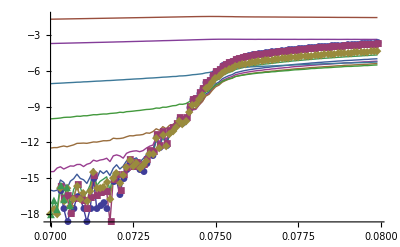

```mathematica
ListLogPlot[{gap1000,gap1001,gap1002,gap1003,gap1004,gap1005,gap1006,gap1007,gap1008,gap1009,gap1010},PlotLegend->{"0","1","2","3","4","5","6","7","8","9","10"},LegendPosition->{1.1,-0.4},LegendShadow->None,Joined->{True},PlotMarkers->Automatic,PlotRange->Full,PlotLabel->"GapDistribution, Vmax=10, 30k"]
```